```mathematica
(M = {{(k + 2*Pi)^2  - x, 0.1k^2, 0}, {0.1(k+2*Pi)^2, k^2 - x,  (k-2*Pi)^2}, {0, 0.1k^2, (k-2*Pi)^2 - x}})// MatrixForm
```

((k+2 π)^2-x | 0.1 k^2 | 0
0.1 (k+2 π)^2 | k^2-x | (k-2 π)^2
0 | 0.1 k^2 | (k-2 π)^2-x)

```mathematica
Mat[k_]:={{0.99(k+2*Pi)^2,0.5 k^2,0},{0.5(k+2*Pi)^2,0.99k^2,0.5(k-2*Pi)^2},{0,0.5 k^2,0.99(k-2*Pi)^2}}
```

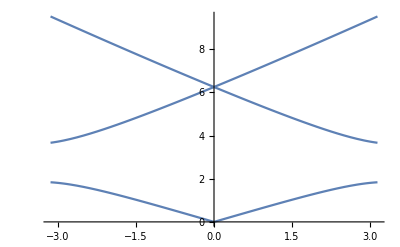

```mathematica
Plot[Sqrt[Eigenvalues[Mat[k]]],{k,-Pi,Pi}]
```

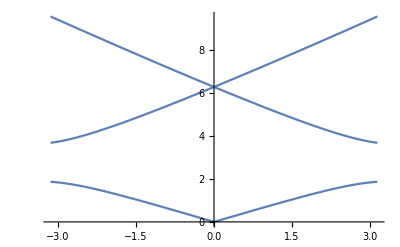

```mathematica
Plot[Sqrt[Eigenvalues[Mat[k]]], {k, -Pi, Pi}]
```

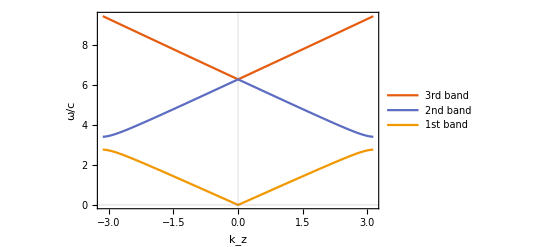

```mathematica
ListPlot[Transpose@Table[Sqrt[Eigenvalues[Mat[t]]],{t,-Pi,Pi,0.01}], 
Joined->True,PlotTheme->"Scientific", DataRange->{-Pi,Pi}, FrameLabel->{Subscript[k,z],"ω/c"}, PlotLegends->{"3rd band","2nd band","1st band"}]
```

```mathematica
Eigenvectors[Mat[0]]
```

{{0.980581,0.196116,0.},{0.,0.196116,0.980581},{0.,1.,0.}}

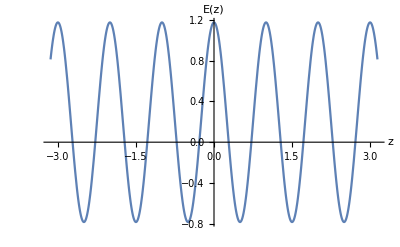

```mathematica
Plot[0Cos[2Pi z] + 0.196116 + 0.980581Cos[-2Pi z], {z, -Pi, Pi}, AxesLabel->{z, "E(z)"}]
```

```mathematica
Eigenvectors[Mat[Pi]]
```

{{-0.975828,-0.218474,-0.00543145},{-0.0170134,0.66537,0.74632},{0.0181065,-0.744458,0.667424}}

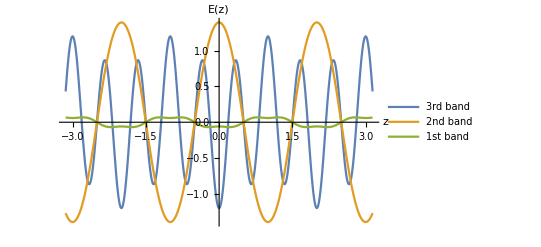

```mathematica
Plot[{-0.975828 Cos[3 Pi z]+-0.218474Cos[Pi z]+-0.00543145 Cos[-Pi z],
-0.0170134 Cos[3 Pi z]+0.66537 Cos[Pi z]+0.74632 Cos[-Pi z], 0.0181065 Cos[3 Pi z]+-0.744458 Cos[Pi z]+0.667424 Cos[-Pi z]},{z,-Pi,Pi}, AxesLabel->{z,"E(z)"}, PlotLegends->{"3rd band", "2nd band", "1st band"}]
```